ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

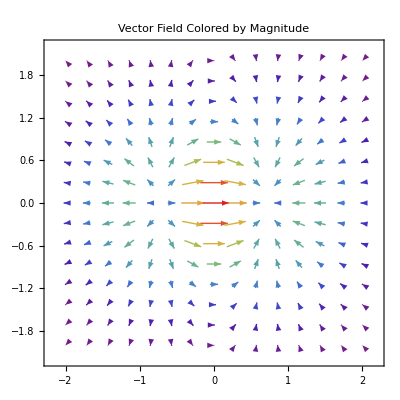

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A[x_,y_]=D[f[x,y],x]
B[x_,y_]=D[f[x,y],y]
ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow"]
VectorPlot[{A[x,y],B[x,y]},{x,-2,2},{y,-2,2},VectorColorFunction->Function[{x,y,u,v,norm},ColorData["Rainbow"][norm]],VectorColorFunctionScaling->True,PlotLabel->"Vector Field Colored by Magnitude"]
```

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A[x_,y_]=D[f[x,y],x]
B[x_,y_]=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic];
plot2=VectorPlot[{A[x,y],B[x,y]},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{-5,5}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,ContourLabels->True,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],(*Setting range in legend may show wrong data from the plot*)ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[Automatic,None],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-